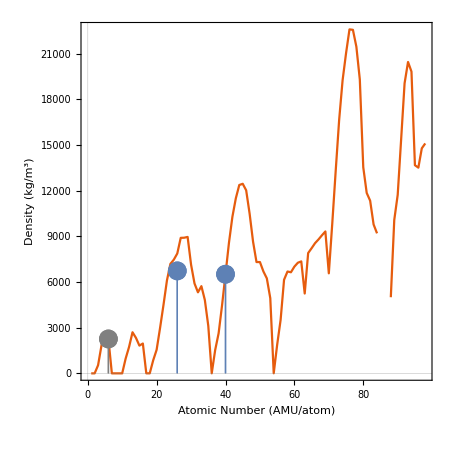

```mathematica
Show[{ListLinePlot[Table[ElementData[z,"Density"],{z,1,118}],PlotTheme->"Scientific",FrameTicksStyle->Directive[20,Black],Frame->True,FrameLabel->{Style["Atomic Number (AMU/atom)",20,Black],Style["Density (kg/m^3)",20,Black]},ImageSize->450,AspectRatio->1],ListPlot[Table[{z,ElementData[z,"Density"]},{z,6,6}],PlotStyle->Directive[Gray,PointSize[0.03]],Filling->Bottom,FillingStyle->Thick],ListPlot[Table[{z,ElementData[z,"Density"]},{z,40,40}],PlotStyle->Directive[PointSize[0.03]],Filling->Bottom,FillingStyle->Thick],ListPlot[{{(12+40)/2,6.73*10^3}},PlotStyle->Directive[PointSize[0.03]],Filling->Bottom,FillingStyle->Thick]}]
```

```mathematica
Show[{ListLogPlot[Table[ElementData[z,"EarthAbundance"],{z,1,118}],PlotTheme->"Scientific",FrameTicksStyle->Directive[20,Black],Frame->True,FrameLabel->{Style["Atomic mass per atom (AMU)",20,Black],Style["Abundance (g/g)",20,Black]},ImageSize->450,AspectRatio->1],ListLogPlot[Table[{z,ElementData[z,"EarthAbundance"]},{z,6,6}],PlotStyle->Directive[Gray,PointSize[0.03]],Filling->Bottom,FillingStyle->Thick],ListLogPlot[Table[{z,ElementData[z,"EarthAbundance"]},{z,40,40}],PlotStyle->Directive[PointSize[0.03]],Filling->Bottom,FillingStyle->Thick]}]
```

$Aborted

```mathematica
ElementData["Properties"]
```

{Abbreviation,AdiabaticIndex,AllotropeNames,AllotropicMultiplicities,AlternateNames,AlternateStandardNames,AtomicMass,AtomicNumber,AtomicRadius,Block,BoilingPoint,BrinellHardness,BulkModulus,CASNumber,Color,CommonCompoundNames,CovalentRadius,CriticalPressure,CriticalTemperature,CrustAbundance,CrystalStructure,CuriePoint,DecayMode,Density,DiscoveryCountries,DiscoveryYear,ElectricalConductivity,ElectricalType,ElectronAffinity,ElectronConfiguration,ElectronConfigurationString,Electronegativity,ElectronShellConfiguration,FusionHeat,GasAtomicMultiplicities,Group,HalfLife,HumanAbundance,IconColor,IonizationEnergies,IsotopeAbundances,KnownIsotopes,LatticeAngles,LatticeConstants,Lifetime,LiquidDensity,MagneticType,MassMagneticSusceptibility,MeltingPoint,Memberships,MeteoriteAbundance,MohsHardness,MolarMagneticSusceptibility,MolarVolume,Name,NeelPoint,NeutronCrossSection,NeutronMassAbsorption,OceanAbundance,Period,Phase,PoissonRatio,QuantumNumbers,Radioactive,RefractiveIndex,Resistivity,Series,ShearModulus,SolarAbundance,SoundSpeed,SpaceGroupName,SpaceGroupNumber,SpecificHeat,StableIsotopes,StandardName,SuperconductingPoint,ThermalConductivity,ThermalExpansion,UniverseAbundance,Valence,VanDerWaalsRadius,VaporizationHeat,VickersHardness,VolumeMagneticSusceptibility,YoungModulus}

```mathematica
ElementData["Properties"]
```

{Abbreviation,AdiabaticIndex,AllotropeNames,AllotropicMultiplicities,AlternateNames,AlternateStandardNames,AtomicMass,AtomicNumber,AtomicRadius,Block,BoilingPoint,BrinellHardness,BulkModulus,CASNumber,Color,CommonCompoundNames,CovalentRadius,CriticalPressure,CriticalTemperature,CrustAbundance,CrystalStructure,CuriePoint,DecayMode,Density,DiscoveryCountries,DiscoveryYear,ElectricalConductivity,ElectricalType,ElectronAffinity,ElectronConfiguration,ElectronConfigurationString,Electronegativity,ElectronShellConfiguration,FusionHeat,GasAtomicMultiplicities,Group,HalfLife,HumanAbundance,IconColor,IonizationEnergies,IsotopeAbundances,KnownIsotopes,LatticeAngles,LatticeConstants,Lifetime,LiquidDensity,MagneticType,MassMagneticSusceptibility,MeltingPoint,Memberships,MeteoriteAbundance,MohsHardness,MolarMagneticSusceptibility,MolarVolume,Name,NeelPoint,NeutronCrossSection,NeutronMassAbsorption,OceanAbundance,Period,Phase,PoissonRatio,QuantumNumbers,Radioactive,RefractiveIndex,Resistivity,Series,ShearModulus,SolarAbundance,SoundSpeed,SpaceGroupName,SpaceGroupNumber,SpecificHeat,StableIsotopes,StandardName,SuperconductingPoint,ThermalConductivity,ThermalExpansion,UniverseAbundance,Valence,VanDerWaalsRadius,VaporizationHeat,VickersHardness,VolumeMagneticSusceptibility,YoungModulus}

```mathematica
densityElasticdata=Table[{ElementData[z,"Density"]/1000,ElementData[z,"YoungModulus"]},{z,1,100}]
```

{{0.0000899 kg/m^3,Missing[NotApplicable]},{0.0001785 kg/m^3,Missing[NotApplicable]},{0.535 kg/m^3,4.9 GPa},{1.848 kg/m^3,287. GPa},{2.46 kg/m^3,Missing[NotAvailable]},{2.26 kg/m^3,Missing[NotAvailable]},{0.001251 kg/m^3,Missing[NotApplicable]},{0.001429 kg/m^3,Missing[NotApplicable]},{0.001696 kg/m^3,Missing[NotApplicable]},{0.0009 kg/m^3,Missing[NotApplicable]},{0.968 kg/m^3,10. GPa},{1.738 kg/m^3,45. GPa},{2.7 kg/m^3,70. GPa},{2.33 kg/m^3,47. GPa},{1.823 kg/m^3,Missing[NotAvailable]},{1.96 kg/m^3,Missing[NotAvailable]},{0.003214 kg/m^3,Missing[NotApplicable]},{0.001784 kg/m^3,Missing[NotApplicable]},{0.856 kg/m^3,Missing[NotAvailable]},{1.55 kg/m^3,20. GPa},{2.985 kg/m^3,74. GPa},{4.507 kg/m^3,116. GPa},{6.11 kg/m^3,128. GPa},{7.19 kg/m^3,279. GPa},{7.47 kg/m^3,198. GPa},{7.874 kg/m^3,211. GPa},{8.9 kg/m^3,209. GPa},{8.908 kg/m^3,200. GPa},{8.96 kg/m^3,130. GPa},{7.14 kg/m^3,108. GPa},{5.904 kg/m^3,Missing[NotAvailable]},{5.323 kg/m^3,Missing[Unknown]},{5.727 kg/m^3,8. GPa},{4.819 kg/m^3,10. GPa},{3.12 kg/m^3,Missing[NotApplicable]},{0.00375 kg/m^3,Missing[NotApplicable]},{1.532 kg/m^3,2.4 GPa},{2.63 kg/m^3,Missing[NotAvailable]},{4.472 kg/m^3,64. GPa},{6.511 kg/m^3,67. GPa},{8.57 kg/m^3,105. GPa},{10.28 kg/m^3,329. GPa},{11.5 kg/m^3,Missing[NotAvailable]},{12.37 kg/m^3,447. GPa},{12.45 kg/m^3,275. GPa},{12.023 kg/m^3,121. GPa},{10.49 kg/m^3,85. GPa},{8.65 kg/m^3,50. GPa},{7.31 kg/m^3,11. GPa},{7.31 kg/m^3,50. GPa},{6.697 kg/m^3,55. GPa},{6.24 kg/m^3,43. GPa},{4.94 kg/m^3,Missing[NotAvailable]},{0.0059 kg/m^3,Missing[NotApplicable]},{1.879 kg/m^3,1.7 GPa},{3.51 kg/m^3,13. GPa},{6.146 kg/m^3,37. GPa},{6.689 kg/m^3,34. GPa},{6.64 kg/m^3,37. GPa},{7.01 kg/m^3,41. GPa},{7.264 kg/m^3,46. GPa},{7.353 kg/m^3,50. GPa},{5.244 kg/m^3,18. GPa},{7.901 kg/m^3,55. GPa},{8.219 kg/m^3,56. GPa},{8.551 kg/m^3,61. GPa},{8.795 kg/m^3,64. GPa},{9.066 kg/m^3,70. GPa},{9.32 kg/m^3,74. GPa},{6.57 kg/m^3,24. GPa},{9.841 kg/m^3,67. GPa},{13.31 kg/m^3,78. GPa},{16.65 kg/m^3,186. GPa},{19.25 kg/m^3,411. GPa},{21.02 kg/m^3,463. GPa},{22.59 kg/m^3,Missing[NotAvailable]},{22.56 kg/m^3,528. GPa},{21.45 kg/m^3,168. GPa},{19.3 kg/m^3,78. GPa},{13.534 kg/m^3,Missing[NotApplicable]},{11.85 kg/m^3,8. GPa},{11.34 kg/m^3,16. GPa},{9.78 kg/m^3,32. GPa},{9.196 kg/m^3,Missing[NotAvailable]},{Missing[NotAvailable]/1000,Missing[NotAvailable]},{0.00973 kg/m^3,Missing[NotAvailable]},{Missing[NotAvailable]/1000,Missing[NotAvailable]},{5. kg/m^3,Missing[NotAvailable]},{10.07 kg/m^3,Missing[NotAvailable]},{11.724 kg/m^3,79. GPa},{15.37 kg/m^3,Missing[Unknown]},{19.05 kg/m^3,208. GPa},{20.45 kg/m^3,Missing[Unknown]},{19.816 kg/m^3,96. GPa},{13.67 kg/m^3,Missing[Unknown]},{13.51 kg/m^3,Missing[Unknown]},{14.78 kg/m^3,Missing[NotAvailable]},{15.1 kg/m^3,Missing[NotAvailable]},{Missing[NotAvailable]/1000,Missing[NotAvailable]},{Missing[NotAvailable]/1000,Missing[NotAvailable]}}

```mathematica
densityMPdata=Table[{ElementData[z,"Density"]/1000,ElementData[z,"MeltingPoint"]},{z,1,100}]
```

{{0.0000899 kg/m^3,-259.14 °C},{0.0001785 kg/m^3,Missing[NotApplicable]},{0.535 kg/m^3,180.54 °C},{1.848 kg/m^3,1287. °C},{2.46 kg/m^3,2075. °C},{2.26 kg/m^3,3550. °C},{0.001251 kg/m^3,-210.1 °C},{0.001429 kg/m^3,-218.3 °C},{0.001696 kg/m^3,-219.6 °C},{0.0009 kg/m^3,-248.59 °C},{0.968 kg/m^3,97.72 °C},{1.738 kg/m^3,650. °C},{2.7 kg/m^3,660.32 °C},{2.33 kg/m^3,1414. °C},{1.823 kg/m^3,44.2 °C},{1.96 kg/m^3,115.21 °C},{0.003214 kg/m^3,-101.5 °C},{0.001784 kg/m^3,-189.3 °C},{0.856 kg/m^3,63.38 °C},{1.55 kg/m^3,842. °C},{2.985 kg/m^3,1541. °C},{4.507 kg/m^3,1668. °C},{6.11 kg/m^3,1910. °C},{7.19 kg/m^3,1907. °C},{7.47 kg/m^3,1246. °C},{7.874 kg/m^3,1538. °C},{8.9 kg/m^3,1495. °C},{8.908 kg/m^3,1455. °C},{8.96 kg/m^3,1084.62 °C},{7.14 kg/m^3,419.53 °C},{5.904 kg/m^3,29.76 °C},{5.323 kg/m^3,938.3 °C},{5.727 kg/m^3,817. °C},{4.819 kg/m^3,221. °C},{3.12 kg/m^3,-7.3 °C},{0.00375 kg/m^3,-157.36 °C},{1.532 kg/m^3,39.31 °C},{2.63 kg/m^3,777. °C},{4.472 kg/m^3,1526. °C},{6.511 kg/m^3,1855. °C},{8.57 kg/m^3,2477. °C},{10.28 kg/m^3,2623. °C},{11.5 kg/m^3,2157. °C},{12.37 kg/m^3,2334. °C},{12.45 kg/m^3,1964. °C},{12.023 kg/m^3,1554.9 °C},{10.49 kg/m^3,961.78 °C},{8.65 kg/m^3,321.07 °C},{7.31 kg/m^3,156.6 °C},{7.31 kg/m^3,231.93 °C},{6.697 kg/m^3,630.63 °C},{6.24 kg/m^3,449.51 °C},{4.94 kg/m^3,113.7 °C},{0.0059 kg/m^3,-111.8 °C},{1.879 kg/m^3,28.44 °C},{3.51 kg/m^3,727. °C},{6.146 kg/m^3,919. °C},{6.689 kg/m^3,798. °C},{6.64 kg/m^3,931. °C},{7.01 kg/m^3,1021. °C},{7.264 kg/m^3,1100. °C},{7.353 kg/m^3,1072. °C},{5.244 kg/m^3,822. °C},{7.901 kg/m^3,1313. °C},{8.219 kg/m^3,1356. °C},{8.551 kg/m^3,1412. °C},{8.795 kg/m^3,1474. °C},{9.066 kg/m^3,1497. °C},{9.32 kg/m^3,1545. °C},{6.57 kg/m^3,819. °C},{9.841 kg/m^3,1663. °C},{13.31 kg/m^3,2233. °C},{16.65 kg/m^3,3017. °C},{19.25 kg/m^3,3422. °C},{21.02 kg/m^3,3186. °C},{22.59 kg/m^3,3033. °C},{22.56 kg/m^3,2466. °C},{21.45 kg/m^3,1768.3 °C},{19.3 kg/m^3,1064.18 °C},{13.534 kg/m^3,-38.83 °C},{11.85 kg/m^3,304. °C},{11.34 kg/m^3,327.46 °C},{9.78 kg/m^3,271.3 °C},{9.196 kg/m^3,254. °C},{Missing[NotAvailable]/1000,302. °C},{0.00973 kg/m^3,-71. °C},{Missing[NotAvailable]/1000,Missing[NotAvailable]},{5. kg/m^3,700. °C},{10.07 kg/m^3,1050. °C},{11.724 kg/m^3,1750. °C},{15.37 kg/m^3,1572. °C},{19.05 kg/m^3,1135. °C},{20.45 kg/m^3,644. °C},{19.816 kg/m^3,640. °C},{13.67 kg/m^3,1176. °C},{13.51 kg/m^3,1345. °C},{14.78 kg/m^3,1050. °C},{15.1 kg/m^3,900. °C},{Missing[NotAvailable]/1000,860. °C},{Missing[NotAvailable]/1000,1527. °C}}

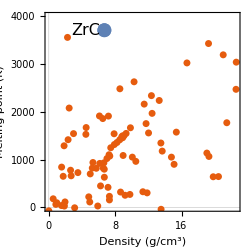

```mathematica
pops={PlotTheme->"Scientific",Frame->True,FrameStyle->Directive[Thickness[0.004]],FrameTicks->{{{0,1000,2000,3000,4000},None},{Automatic,Automatic}},FrameTicksStyle->Directive[20,Black],PlotRange->{{0,Automatic},{0,3990}},FrameLabel->{Style["Density (g/cm^3)",18,Black],Style["Melting point (K)",18,Black]},PlotStyle->Directive[PointSize[0.02]],ImageSize->350};
p1=Show[{ListPlot[densityMPdata,Evaluate@pops],ListPlot[{{6.7,3700}},PlotLabels->Placed[{Style["ZrC",16,Black,FontFamily->Times]},Right],PlotStyle->Directive[PointSize[0.04]]]},AspectRatio->1,ImageSize->250]
```

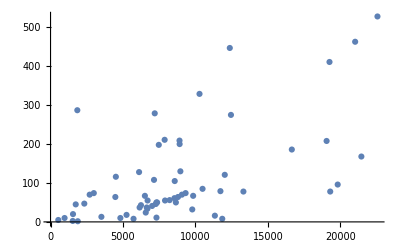

```mathematica
ListPlot[densityElasticdata]
```

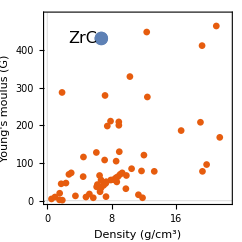

```mathematica
pops2={PlotTheme->"Scientific",Frame->True,FrameStyle->Directive[Thickness[0.004]],FrameTicks->{{Automatic,None},{Automatic,Automatic}},FrameTicksStyle->Directive[20,Black],PlotRange->{{0,Automatic},{0,490}},FrameLabel->{Style["Density (g/cm^3)",18,Black],Style["Young's moulus (G)",18,Black]},PlotStyle->Directive[PointSize[0.02]],ImageSize->350};
p2=Show[{ListPlot[densityElasticdata,Evaluate@pops2],ListPlot[{{6.73,430}},PlotLabels->Placed[{Style["ZrC",16,Black,FontFamily->Times]},Right],PlotStyle->Directive[PointSize[0.04]]]},AspectRatio->1,ImageSize->242]
```

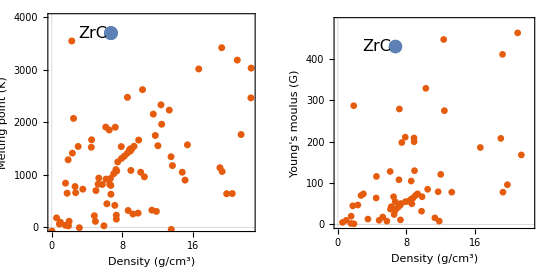

```mathematica
youngMPdens=GraphicsGrid[{{p1,p2}}]
```

```mathematica
Export["/Users/tom/Documents/Lyx_documents/ZrC_transport_paper/images/Young-MP-density.pdf",youngMPdens]
```

/Users/tom/Documents/Lyx_documents/ZrC_transport_paper/images/Young-MP-density.pdf

```mathematica
Correlation@densityMPdata
```

$Aborted

```mathematica
Table[{z,ElementData[z,"Name"],ElementData[z,"YoungModulus"],ElementData[z,"Resistivity"],ElementData[z,"Density"],ElementData[z,"MeltingPoint"]},{z,1,118}]//TableForm
```

1 | hydrogen | Missing[NotApplicable] | Missing[NotApplicable] | 0.0899 kg/m^3 | -259.14 °C
2 | helium | Missing[NotApplicable] | Missing[NotApplicable] | 0.1785 kg/m^3 | Missing[NotApplicable]
3 | lithium | 4.9 GPa | 9.4×10^-8 m Ω | 535. kg/m^3 | 180.54 °C
4 | beryllium | 287. GPa | 4.×10^-8 m Ω | 1848. kg/m^3 | 1287. °C
5 | boron | Missing[NotAvailable] | 10000. m Ω | 2460. kg/m^3 | 2075. °C
6 | carbon | Missing[NotAvailable] | 0.00001 m Ω | 2260. kg/m^3 | 3550. °C
7 | nitrogen | Missing[NotApplicable] | Missing[NotApplicable] | 1.251 kg/m^3 | -210.1 °C
8 | oxygen | Missing[NotApplicable] | Missing[NotApplicable] | 1.429 kg/m^3 | -218.3 °C
9 | fluorine | Missing[NotApplicable] | Missing[NotApplicable] | 1.696 kg/m^3 | -219.6 °C
10 | neon | Missing[NotApplicable] | Missing[NotApplicable] | 0.9 kg/m^3 | -248.59 °C
11 | sodium | 10. GPa | 4.7×10^-8 m Ω | 968. kg/m^3 | 97.72 °C
12 | magnesium | 45. GPa | 4.4×10^-8 m Ω | 1738. kg/m^3 | 650. °C
13 | aluminum | 70. GPa | 2.6×10^-8 m Ω | 2700. kg/m^3 | 660.32 °C
14 | silicon | 47. GPa | 0.001 m Ω | 2330. kg/m^3 | 1414. °C
15 | phosphorus | Missing[NotAvailable] | 1.×10^-7 m Ω | 1823. kg/m^3 | 44.2 °C
16 | sulfur | Missing[NotAvailable] | 1.×10^15 m Ω | 1960. kg/m^3 | 115.21 °C
17 | chlorine | Missing[NotApplicable] | 100. m Ω | 3.214 kg/m^3 | -101.5 °C
18 | argon | Missing[NotApplicable] | Missing[NotApplicable] | 1.784 kg/m^3 | -189.3 °C
19 | potassium | Missing[NotAvailable] | 7.×10^-8 m Ω | 856. kg/m^3 | 63.38 °C
20 | calcium | 20. GPa | 3.4×10^-8 m Ω | 1550. kg/m^3 | 842. °C
21 | scandium | 74. GPa | 5.5×10^-7 m Ω | 2985. kg/m^3 | 1541. °C
22 | titanium | 116. GPa | 4.×10^-7 m Ω | 4507. kg/m^3 | 1668. °C
23 | vanadium | 128. GPa | 2.×10^-7 m Ω | 6110. kg/m^3 | 1910. °C
24 | chromium | 279. GPa | 1.3×10^-7 m Ω | 7190. kg/m^3 | 1907. °C
25 | manganese | 198. GPa | 1.6×10^-6 m Ω | 7470. kg/m^3 | 1246. °C
26 | iron | 211. GPa | 9.7×10^-8 m Ω | 7874. kg/m^3 | 1538. °C
27 | cobalt | 209. GPa | 6.×10^-8 m Ω | 8900. kg/m^3 | 1495. °C
28 | nickel | 200. GPa | 7.×10^-8 m Ω | 8908. kg/m^3 | 1455. °C
29 | copper | 130. GPa | 1.7×10^-8 m Ω | 8960. kg/m^3 | 1084.62 °C
30 | zinc | 108. GPa | 5.9×10^-8 m Ω | 7140. kg/m^3 | 419.53 °C
31 | gallium | Missing[NotAvailable] | 1.4×10^-7 m Ω | 5904. kg/m^3 | 29.76 °C
32 | germanium | Missing[Unknown] | 0.0005 m Ω | 5323. kg/m^3 | 938.3 °C
33 | arsenic | 8. GPa | 3.×10^-7 m Ω | 5727. kg/m^3 | 817. °C
34 | selenium | 10. GPa | Missing[NotAvailable] | 4819. kg/m^3 | 221. °C
35 | bromine | Missing[NotApplicable] | 1.×10^10 m Ω | 3120. kg/m^3 | -7.3 °C
36 | krypton | Missing[NotApplicable] | Missing[NotApplicable] | 3.75 kg/m^3 | -157.36 °C
37 | rubidium | 2.4 GPa | 1.2×10^-7 m Ω | 1532. kg/m^3 | 39.31 °C
38 | strontium | Missing[NotAvailable] | 1.3×10^-7 m Ω | 2630. kg/m^3 | 777. °C
39 | yttrium | 64. GPa | 5.7×10^-7 m Ω | 4472. kg/m^3 | 1526. °C
40 | zirconium | 67. GPa | 4.2×10^-7 m Ω | 6511. kg/m^3 | 1855. °C
41 | niobium | 105. GPa | 1.5×10^-7 m Ω | 8570. kg/m^3 | 2477. °C
42 | molybdenum | 329. GPa | 5.×10^-8 m Ω | 10280. kg/m^3 | 2623. °C
43 | technetium | Missing[NotAvailable] | 2.×10^-7 m Ω | 11500. kg/m^3 | 2157. °C
44 | ruthenium | 447. GPa | 7.×10^-8 m Ω | 12370. kg/m^3 | 2334. °C
45 | rhodium | 275. GPa | 4.3×10^-8 m Ω | 12450. kg/m^3 | 1964. °C
46 | palladium | 121. GPa | 1.×10^-7 m Ω | 12023. kg/m^3 | 1554.9 °C
47 | silver | 85. GPa | 1.6×10^-8 m Ω | 10490. kg/m^3 | 961.78 °C
48 | cadmium | 50. GPa | 7.×10^-8 m Ω | 8650. kg/m^3 | 321.07 °C
49 | indium | 11. GPa | 8.×10^-8 m Ω | 7310. kg/m^3 | 156.6 °C
50 | tin | 50. GPa | 1.1×10^-7 m Ω | 7310. kg/m^3 | 231.93 °C
51 | antimony | 55. GPa | 4.×10^-7 m Ω | 6697. kg/m^3 | 630.63 °C
52 | tellurium | 43. GPa | 0.0001 m Ω | 6240. kg/m^3 | 449.51 °C
53 | iodine | Missing[NotAvailable] | 1.×10^7 m Ω | 4940. kg/m^3 | 113.7 °C
54 | xenon | Missing[NotApplicable] | Missing[NotApplicable] | 5.9 kg/m^3 | -111.8 °C
55 | cesium | 1.7 GPa | 2.×10^-7 m Ω | 1879. kg/m^3 | 28.44 °C
56 | barium | 13. GPa | 3.5×10^-7 m Ω | 3510. kg/m^3 | 727. °C
57 | lanthanum | 37. GPa | 6.1×10^-7 m Ω | 6146. kg/m^3 | 919. °C
58 | cerium | 34. GPa | 7.5×10^-7 m Ω | 6689. kg/m^3 | 798. °C
59 | praseodymium | 37. GPa | 7.×10^-7 m Ω | 6640. kg/m^3 | 931. °C
60 | neodymium | 41. GPa | 6.4×10^-7 m Ω | 7010. kg/m^3 | 1021. °C
61 | promethium | 46. GPa | 7.5×10^-7 m Ω | 7264. kg/m^3 | 1100. °C
62 | samarium | 50. GPa | 9.4×10^-7 m Ω | 7353. kg/m^3 | 1072. °C
63 | europium | 18. GPa | 9.×10^-7 m Ω | 5244. kg/m^3 | 822. °C
64 | gadolinium | 55. GPa | 1.3×10^-6 m Ω | 7901. kg/m^3 | 1313. °C
65 | terbium | 56. GPa | 1.2×10^-6 m Ω | 8219. kg/m^3 | 1356. °C
66 | dysprosium | 61. GPa | 9.1×10^-7 m Ω | 8551. kg/m^3 | 1412. °C
67 | holmium | 64. GPa | 9.4×10^-7 m Ω | 8795. kg/m^3 | 1474. °C
68 | erbium | 70. GPa | 8.6×10^-7 m Ω | 9066. kg/m^3 | 1497. °C
69 | thulium | 74. GPa | 7.×10^-7 m Ω | 9320. kg/m^3 | 1545. °C
70 | ytterbium | 24. GPa | 2.8×10^-7 m Ω | 6570. kg/m^3 | 819. °C
71 | lutetium | 67. GPa | 5.7×10^-7 m Ω | 9841. kg/m^3 | 1663. °C
72 | hafnium | 78. GPa | 3.×10^-7 m Ω | 13310. kg/m^3 | 2233. °C
73 | tantalum | 186. GPa | 1.3×10^-7 m Ω | 16650. kg/m^3 | 3017. °C
74 | tungsten | 411. GPa | 5.×10^-8 m Ω | 19250. kg/m^3 | 3422. °C
75 | rhenium | 463. GPa | 1.8×10^-7 m Ω | 21020. kg/m^3 | 3186. °C
76 | osmium | Missing[NotAvailable] | 8.×10^-8 m Ω | 22590. kg/m^3 | 3033. °C
77 | iridium | 528. GPa | 4.7×10^-8 m Ω | 22560. kg/m^3 | 2466. °C
78 | platinum | 168. GPa | 1.1×10^-7 m Ω | 21450. kg/m^3 | 1768.3 °C
79 | gold | 78. GPa | 2.2×10^-8 m Ω | 19300. kg/m^3 | 1064.18 °C
80 | mercury | Missing[NotApplicable] | 9.6×10^-7 m Ω | 13534. kg/m^3 | -38.83 °C
81 | thallium | 8. GPa | 1.5×10^-7 m Ω | 11850. kg/m^3 | 304. °C
82 | lead | 16. GPa | 2.1×10^-7 m Ω | 11340. kg/m^3 | 327.46 °C
83 | bismuth | 32. GPa | 1.3×10^-6 m Ω | 9780. kg/m^3 | 271.3 °C
84 | polonium | Missing[NotAvailable] | 4.3×10^-7 m Ω | 9196. kg/m^3 | 254. °C
85 | astatine | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable] | 302. °C
86 | radon | Missing[NotAvailable] | Missing[NotApplicable] | 9.73 kg/m^3 | -71. °C
87 | francium | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
88 | radium | Missing[NotAvailable] | 1.×10^-6 m Ω | 5000. kg/m^3 | 700. °C
89 | actinium | Missing[NotAvailable] | Missing[NotAvailable] | 10070. kg/m^3 | 1050. °C
90 | thorium | 79. GPa | 1.5×10^-7 m Ω | 11724. kg/m^3 | 1750. °C
91 | protactinium | Missing[Unknown] | 1.8×10^-7 m Ω | 15370. kg/m^3 | 1572. °C
92 | uranium | 208. GPa | 2.8×10^-7 m Ω | 19050. kg/m^3 | 1135. °C
93 | neptunium | Missing[Unknown] | 1.2×10^-6 m Ω | 20450. kg/m^3 | 644. °C
94 | plutonium | 96. GPa | 1.5×10^-6 m Ω | 19816. kg/m^3 | 640. °C
95 | americium | Missing[Unknown] | Missing[Unknown] | 13670. kg/m^3 | 1176. °C
96 | curium | Missing[Unknown] | Missing[Unknown] | 13510. kg/m^3 | 1345. °C
97 | berkelium | Missing[NotAvailable] | Missing[NotAvailable] | 14780. kg/m^3 | 1050. °C
98 | californium | Missing[NotAvailable] | Missing[NotAvailable] | 15100. kg/m^3 | 900. °C
99 | einsteinium | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable] | 860. °C
100 | fermium | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable] | 1527. °C
101 | mendelevium | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable] | 828. °C
102 | nobelium | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable] | 828. °C
103 | lawrencium | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable] | 1627. °C
104 | rutherfordium | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
105 | dubnium | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
106 | seaborgium | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
107 | bohrium | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
108 | hassium | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
109 | meitnerium | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
110 | darmstadtium | Missing[Unknown] | Missing[Unknown] | Missing[Unknown] | Missing[Unknown]
111 | roentgenium | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
112 | copernicium | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
113 | ununtrium | Missing[Unknown] | Missing[Unknown] | Missing[Unknown] | Missing[Unknown]
114 | flerovium | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
115 | ununpentium | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
116 | livermorium | Missing[Unknown] | Missing[Unknown] | Missing[Unknown] | Missing[Unknown]
117 | ununseptium | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]
118 | ununoctium | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable] | Missing[NotAvailable]

```mathematica
Table[ElementData[z,"Density"],{z,1,118}]//Table
```

{0.0899 kg/m^3,0.1785 kg/m^3,535. kg/m^3,1848. kg/m^3,2460. kg/m^3,2260. kg/m^3,1.251 kg/m^3,1.429 kg/m^3,1.696 kg/m^3,0.9 kg/m^3,968. kg/m^3,1738. kg/m^3,2700. kg/m^3,2330. kg/m^3,1823. kg/m^3,1960. kg/m^3,3.214 kg/m^3,1.784 kg/m^3,856. kg/m^3,1550. kg/m^3,2985. kg/m^3,4507. kg/m^3,6110. kg/m^3,7190. kg/m^3,7470. kg/m^3,7874. kg/m^3,8900. kg/m^3,8908. kg/m^3,8960. kg/m^3,7140. kg/m^3,5904. kg/m^3,5323. kg/m^3,5727. kg/m^3,4819. kg/m^3,3120. kg/m^3,3.75 kg/m^3,1532. kg/m^3,2630. kg/m^3,4472. kg/m^3,6511. kg/m^3,8570. kg/m^3,10280. kg/m^3,11500. kg/m^3,12370. kg/m^3,12450. kg/m^3,12023. kg/m^3,10490. kg/m^3,8650. kg/m^3,7310. kg/m^3,7310. kg/m^3,6697. kg/m^3,6240. kg/m^3,4940. kg/m^3,5.9 kg/m^3,1879. kg/m^3,3510. kg/m^3,6146. kg/m^3,6689. kg/m^3,6640. kg/m^3,7010. kg/m^3,7264. kg/m^3,7353. kg/m^3,5244. kg/m^3,7901. kg/m^3,8219. kg/m^3,8551. kg/m^3,8795. kg/m^3,9066. kg/m^3,9320. kg/m^3,6570. kg/m^3,9841. kg/m^3,13310. kg/m^3,16650. kg/m^3,19250. kg/m^3,21020. kg/m^3,22590. kg/m^3,22560. kg/m^3,21450. kg/m^3,19300. kg/m^3,13534. kg/m^3,11850. kg/m^3,11340. kg/m^3,9780. kg/m^3,9196. kg/m^3,Missing[NotAvailable],9.73 kg/m^3,Missing[NotAvailable],5000. kg/m^3,10070. kg/m^3,11724. kg/m^3,15370. kg/m^3,19050. kg/m^3,20450. kg/m^3,19816. kg/m^3,13670. kg/m^3,13510. kg/m^3,14780. kg/m^3,15100. kg/m^3,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[Unknown],Missing[NotAvailable],Missing[NotAvailable],Missing[Unknown],Missing[NotAvailable],Missing[NotAvailable],Missing[Unknown],Missing[NotAvailable],Missing[NotAvailable]}

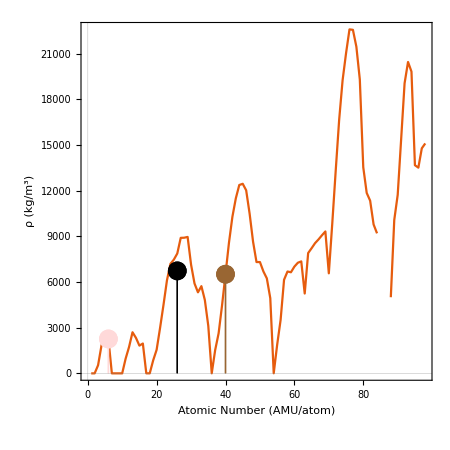

```mathematica
Show[{ListLinePlot[Table[ElementData[z,"Density"],{z,1,118}],PlotTheme->"Scientific",FrameTicksStyle->Directive[20,White],Frame->True,FrameLabel->{Style["Atomic Number (AMU/atom)",20,White],Style["ρ (kg/m^3)",20,White]},ImageSize->450,AspectRatio->1],ListPlot[Table[{z,ElementData[z,"Density"]},{z,6,6}],PlotStyle->Directive[LightRed,PointSize[0.03]],Filling->Bottom,FillingStyle->Thick],ListPlot[Table[{z,ElementData[z,"Density"]},{z,40,40}],PlotStyle->Directive[Brown,PointSize[0.03]],Filling->Bottom,FillingStyle->Thick],ListPlot[{{(12+40)/2,6.73*10^3}},PlotStyle->Directive[Black,PointSize[0.03]],Filling->Bottom,FillingStyle->Thick]}]
```

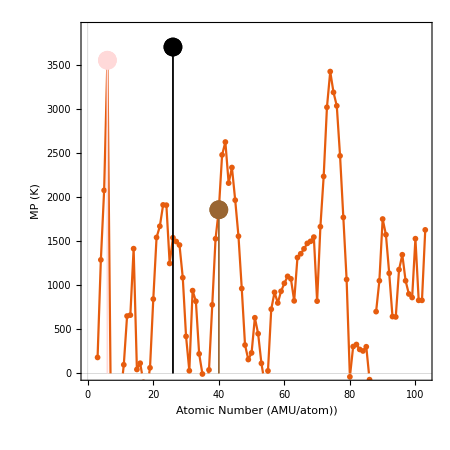

```mathematica
Show[{ListPlot[Table[ElementData[z,"MeltingPoint"],{z,1,118}],PlotTheme->"Scientific",FrameTicksStyle->Directive[20,White],Frame->True,FrameLabel->{Style["Atomic Number (AMU/atom))",20,White],Style["MP (K)",20,White]},ImageSize->450,AspectRatio->1,PlotRange->{Automatic,{0,3900}}],ListLinePlot[Table[ElementData[z,"MeltingPoint"],{z,1,118}],PlotTheme->"Scientific",FrameTicksStyle->Directive[20,White],Frame->True,FrameLabel->{Style["Atomic Number (AMU/atom)",20,White],Style["MP (K)",20,White]},ImageSize->450,AspectRatio->1,PlotRange->{Automatic,{0,3900}}],ListPlot[Table[{z,ElementData[z,"MeltingPoint"]},{z,6,6}],PlotStyle->Directive[LightRed,PointSize[0.03]],Filling->Bottom,FillingStyle->Thick],ListPlot[Table[{z,ElementData[z,"MeltingPoint"]},{z,40,40}],PlotStyle->Directive[Brown,PointSize[0.03]],Filling->Bottom,FillingStyle->Thick],ListPlot[{{(12+40)/2,(3700)}},PlotStyle->Directive[Black,PointSize[0.03]],Filling->Bottom,FillingStyle->Thick]}]
```

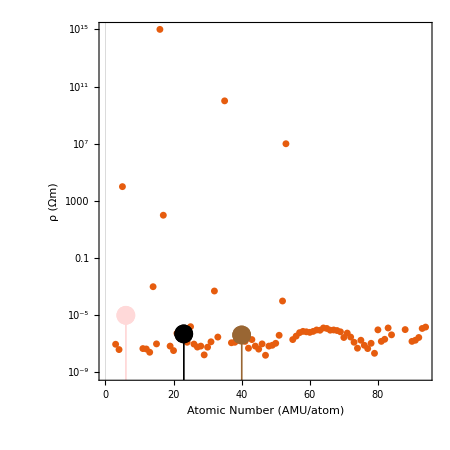

```mathematica
Show[{ListLogPlot[Table[{z,ElementData[z,"Resistivity"]},{z,1,118}],PlotTheme->"Scientific",FrameTicksStyle->Directive[20,White],Frame->True,FrameLabel->{Style["Atomic Number (AMU/atom)",20,White],Style["ρ (Ωm)",20,White]},ImageSize->450,AspectRatio->1],ListLogPlot[Table[{z,ElementData[z,"Resistivity"]},{z,6,6}],PlotStyle->Directive[LightRed,PointSize[0.03]],Filling->Bottom,FillingStyle->Thick],ListLogPlot[Table[{z,ElementData[z,"Resistivity"]},{z,40,40}],PlotStyle->Directive[Brown,PointSize[0.03]],Filling->Bottom,FillingStyle->Thick],ListLogPlot[{{(6+40)/2,(0.5*10^-6)}},Filling->Bottom,PlotStyle->Directive[Black,PointSize[0.03]],FillingStyle->Thick]}]
```

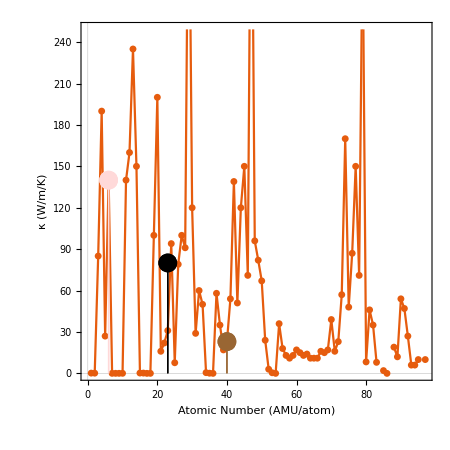

```mathematica
Show[{ListPlot[Table[ElementData[z,"ThermalConductivity"],{z,1,118}],PlotTheme->"Scientific",FrameTicksStyle->Directive[20,White],Frame->True,FrameLabel->{Style["Atomic Number (AMU/atom)",20,White],Style["κ (W/m/K)",20,White]},ImageSize->450,AspectRatio->1],ListLinePlot[Table[ElementData[z,"ThermalConductivity"],{z,1,118}],PlotTheme->"Scientific",FrameTicksStyle->Directive[20,White],Frame->True,FrameLabel->{Style["Atomic Number (AMU/atom)",20,White],Style["κ (W/m/K)",20,White]},ImageSize->450,AspectRatio->1],ListPlot[Table[{z,ElementData[z,"ThermalConductivity"]},{z,6,6}],PlotStyle->Directive[LightRed,PointSize[0.03]],Filling->Bottom,FillingStyle->Thick],ListPlot[Table[{z,ElementData[z,"ThermalConductivity"]},{z,40,40}],PlotStyle->Directive[Brown,PointSize[0.03]],Filling->Bottom,FillingStyle->Thick],ListPlot[{{(6+40)/2,(80)}},Filling->Bottom,PlotStyle->Directive[Black,PointSize[0.03]],FillingStyle->Thick]}]
```

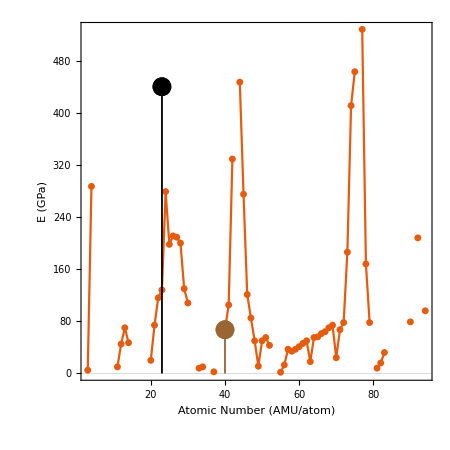

```mathematica
Show[{ListPlot[Table[ElementData[z,"YoungModulus"],{z,1,118}],PlotTheme->"Scientific",FrameTicksStyle->Directive[20,White],Frame->True,FrameLabel->{Style["Atomic Number (AMU/atom)",20,White],Style["E (GPa)",20,White]},ImageSize->450,PlotRange->All,AspectRatio->1],ListLinePlot[Table[ElementData[z,"YoungModulus"],{z,1,118}],PlotTheme->"Scientific",FrameTicksStyle->Directive[20,White],Frame->True,FrameLabel->{Style["Atomic Number (AMU/atom)",20,White],Style["E (GPa)",20,White]},ImageSize->450,PlotRange->All,AspectRatio->1],ListPlot[Table[{z,ElementData[z,"YoungModulus"]},{z,6,6}],PlotStyle->Directive[LightRed,PointSize[0.03]],Filling->Bottom,FillingStyle->Thick],ListPlot[Table[{z,ElementData[z,"YoungModulus"]},{z,40,40}],PlotStyle->Directive[Brown,PointSize[0.03]],Filling->Bottom,FillingStyle->Thick],ListPlot[{{(6+40)/2,(440)}},Filling->Bottom,PlotStyle->Directive[Black,PointSize[0.03]],FillingStyle->Thick]}]
```

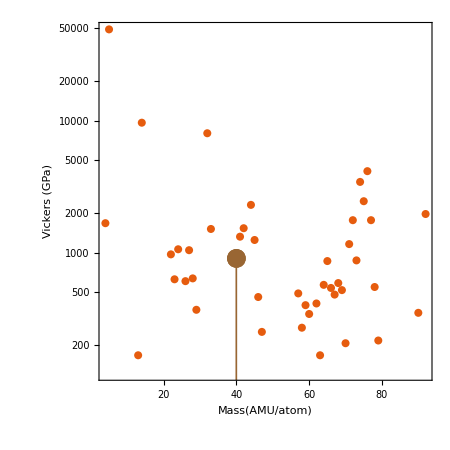

```mathematica
Show[{ListLogPlot[Table[ElementData[z,"VickersHardness"],{z,1,118}],PlotTheme->"Scientific",FrameTicksStyle->Directive[20,White],Frame->True,FrameLabel->{Style["Mass(AMU/atom)",20,White],Style["Vickers (GPa)",20,White]},ImageSize->450,PlotRange->All,AspectRatio->1],ListLogPlot[Table[{z,ElementData[z,"VickersHardness"]},{z,6,6}],PlotStyle->Directive[LightRed,PointSize[0.03]],Filling->Bottom,FillingStyle->Thick],ListLogPlot[Table[{z,ElementData[z,"VickersHardness"]},{z,40,40}],PlotStyle->Directive[Brown,PointSize[0.03]],Filling->Bottom,FillingStyle->Thick],ListLogPlot[{{(12+40)/2,(25)}},Filling->Bottom,PlotStyle->Directive[Black,PointSize[0.03]],FillingStyle->Thick]}]
```

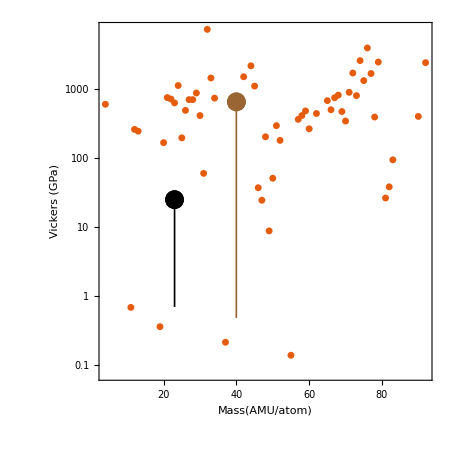

```mathematica
Show[{ListLogPlot[Table[ElementData[z,"BrinellHardness"],{z,1,118}],PlotTheme->"Scientific",FrameTicksStyle->Directive[20,White],Frame->True,FrameLabel->{Style["Mass(AMU/atom)",20,White],Style["Vickers (GPa)",20,White]},ImageSize->450,PlotRange->All,AspectRatio->1],ListLogPlot[Table[{z,ElementData[z,"BrinellHardness"]},{z,6,6}],PlotStyle->Directive[LightRed,PointSize[0.03]],Filling->Bottom,FillingStyle->Thick],ListLogPlot[Table[{z,ElementData[z,"BrinellHardness"]},{z,40,40}],PlotStyle->Directive[Brown,PointSize[0.03]],Filling->Bottom,FillingStyle->Thick],ListLogPlot[{{(6+40)/2,(25)}},Filling->Bottom,PlotStyle->Directive[Black,PointSize[0.03]],FillingStyle->Thick]}]
```

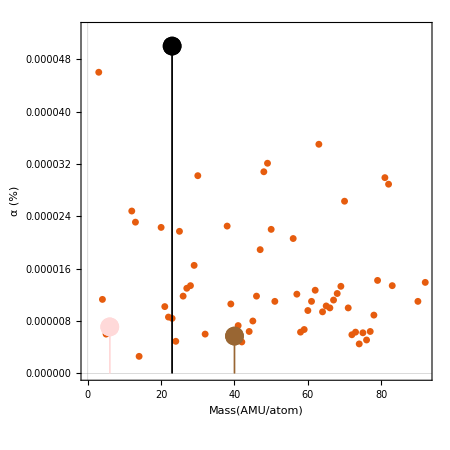

```mathematica
Show[{ListPlot[Table[ElementData[z,"ThermalExpansion"],{z,1,118}],PlotTheme->"Scientific",FrameTicksStyle->Directive[20,White],Frame->True,FrameLabel->{Style["Mass(AMU/atom)",20,White],Style["α (%)",20,White]},ImageSize->450,AspectRatio->1],ListPlot[Table[{z,ElementData[z,"ThermalExpansion"]},{z,6,6}],PlotStyle->Directive[LightRed,PointSize[0.03]],Filling->Bottom,FillingStyle->Thick],ListPlot[Table[{z,ElementData[z,"ThermalExpansion"]},{z,40,40}],PlotStyle->Directive[Brown,PointSize[0.03]],Filling->Bottom,FillingStyle->Thick],ListPlot[{{(6+40)/2,(0.00005)}},Filling->Bottom,PlotStyle->Directive[Black,PointSize[0.03]],FillingStyle->Thick]}]
```